I don’t know whethere I should go or not. Safety issues are worked out. I mean, I can go. It’s just for 2 days, new experiences are also important.

10:00 - 12:00 (Project)

12:00 -

Let’s do ifzero

Let’s start working here

Connection.

Start doing the assignment at 1. Finish some stuff till4

data ast  = 	   num
		 	 	|	 	var
		 	 	|	 	(Bin “+“ expr expr)
		 	 	|    (sub1 expr)
		 	 	|	 	(Fun (var) expr)
		 	 	|	 	(App ast ast)
		 	 	|	 	(IfZero ast ast ast)
		 	 	|	 	(Rec ((var expr)) expr)

maybe we don;’t need rec--the y combinator will work. maybe I can do some “destruction procedure”.

maybe there is no direct conversion. That;s weird.

We can implement multiple subtraction using tail recursion andIfzero. So, that will happen in the parsing stage.

Are if statements functional? I don’t think so. but they can be made to be so.

We should also develop the theory.  So it is just in the end a bunch of rules. That’s a nice way of thinking of things. Yes, that will be very nice to understand. Yes, that is what a Hypergraph Rewriting System is.

However, let’s understand what subtraction is. But the configuration should be different.

This is basically composition. Yes, what is subtraction? Well, we should be able to write code in a loop that does it for us, right? Like, yeah. For example, 9- 7 is just 9-1, then -1 again. This can be done using recursion. So yes. This is going to be very hard. So let’s fuck subtraction for now.

There’s also the implementation of with, which is just function application. I don’t know how to implement that, because my implementation is not much like stack frames. I mean, first I am making compile Aexp and compile Bexp.

Let’s do this quite quickly.

```mathematica
FauxRacketCyclicGraph[n_]:= If[n == 0, {{0,0}}, If[n> 0, cyclicgraph[2 n], cyclicgraph[2 (-n) + 1]]]
```

```mathematica
FauxRacketAddition[]
```

```mathematica
ResourceFunction["WolframModelPlot"][FauxRacketCyclicGraph[-10],VertexLabels->Automatic]
```

Addition rule will apply iff the state attached to the first one is 0 and  both are cyclic graphs. I.e state 0 and state 1 will be used iff addition is used.  We make distinctions because of the semantics. So addition is only defined once we have 2 cyclic graphs connected together in some way.

Adsorption between graphs G_1 and G_2 will happen iff the both graphs have state 2 connected to them. So this has to be very unique. And so we can connect one state (the waiting computation)...I don;t know. there must be a way to formalise all these things.

Also, here create the new states and don’t make the laptop go crazy

Let’s implement subtraction later. Unless...Yes, this

Multiplication between graphs will take place iff the states attached are state 3 attached to them at each transition point. And then state 4 is attached as well afterwards plus subtraction.

How are negative numbers implemented? We can use hypredeges instead or something. Maybe, we can just use the bijection between the numbers or anythign else. Like yes, that migth mean that integers, yes, the bijection is that n ↦  2 n, -n ↦  2(-n) +1. This is a bijection. So a cyclic graph will just have even number of vertices. We have to makes sure that addition is implemented iff we have this marker essentially. So addition iff we have the 0 marker attached. And if we add 2 positive numbers, say 10 and 5, we get 15. So this is just ordinary addition. If we had 10 and -4, then we get should get 6. we have a graph of vertex number 20 and 9. So essentially it’s subtracting and adding 1. If we had add[-10,-4], then we get -14. we have vertex numbers 21 and 9, and we should get vertex numbers 29. So we have to add and subtract 1. If we have subtraction, we just implemented that using addition and not care about anything. So here, we might have differnet rules for negative adn positive and also different initial conditions, but we just need to make sure that we are performing the act of addition when addition is required. But we can have different semantics. But the syntax of language can mean we don’t know when something is negative or positive. so yes. So

We can implement subtraction. But negative numbers are really hard.  This is because addition has one rule and there is no way of knowing whether something is positive or negative firsthand. so   yes. But if we make sure that program never gets a negative numebre,m then it will work.

So, let’s stick to positive numbers

### Applicative order compiler

data Ast  = 	   num
		 	 	|	 	(Bin “+“ expr expr)
		 	 	|    (Sub1 expr)
		 	 	|	 	(Fun (var) expr)
		 	 	|	 	(App ast ast var)
		 	 	|	 	(IfZero ast ast ast)
		 	 	|	 	(Rec ((var expr)) expr)

#### Parser

Perform alpha reduction here!

expr	 	=  num
 	 	|	 	var
 	 	|	 	(+ expr expr)
 	 	|	 	(* expr expr)
 	 	|	 	(- expr expr)
 	 	|	 	(fun (var) expr)
 	 	|	 	(expr expr)
 	 	|	 	(ifzero expr expr expr)
 	 	|	 	(with ((var expr)) expr)
 	 	|	 	(rec ((var expr)) expr)

#### Normal order evaluator.

Well, let’s just assume that we don’t just compile functions . I mean, I think we can.

If I can find a  good pattern matcher, then this talk will become very easy

```mathematica
Clear[compileBin]
```

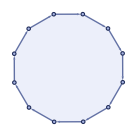

```mathematica
ResourceFunction["WolframModelPlot"][linkingHyperedge]
```

We can create a more interesting shape that is pretty cool!

```mathematica
stateGraph[n_]:= Join[Table[{i,i},{i,1,n+3}],Table[{i,i+1},{i,1,n+3-1}],{{n+3,1}}]
```

```mathematica
JoinState[n_,m_,stateF_]:= Join[ReplaceAll[stateGraph[stateF],Table[i->n+i,{i,1,stateF + 3}]],{{stateF + 3+n ,m }}]
```

```mathematica
seeEvol[{a_,b_},t_]:= ResourceFunction["WolframModel"][Flatten[Symbol[#] &/@ b,1], a,t][ "StatesPlotsList"]
```

```mathematica
startLink[ n_, sizeLinkingHyperedge_]:= {Join[{1},Range[n, n+sizeLinkingHyperedge-2],{1}]}
```

```mathematica
linkingHyperedge= {{1,2,3,4,5,6,7,8,9,10,11,12,1}};
```

```mathematica
linkingHyperedge2 = {{1,2,3,1}};
```

```mathematica
sizeLinkingHyperedge2 = 3;
```

```mathematica
sizeLinkingHyperedge = 12;
```

```mathematica
add = {{{2,1},{2,3},{4,3},{5,5},{6,6},{7,7},{5,6},{6,7},{7,5},{7,2}}->
{{4,1},{2,3},{5,5},{6,6},{7,7},{8,8},{5,6},{6,7},{7,8},{8,5},{8,2}},
{{1,2},{2,3},{4,4},{5,5},{6,6},{7,7},{4,5},{5,6},{6,7},{7,4},{7,1}}->{{1,3}}};
```

```mathematica
addAdsorp2 ={Join[{{1,2},{1,4},{3,4}}, JoinState[4, 1, 2]]-> Join[{{3,2},{1,4}}, JoinState[4,1,3]], Join[{{1,2},{2,3}}, JoinState[3,1,3]]-> Join[{{1,3}},JoinState[3,1,4]], Join[linkingHyperedge,{{1,sizeLinkingHyperedge+1},{sizeLinkingHyperedge+2, 1}}, JoinState[sizeLinkingHyperedge+2, 1, 4]] -> {{sizeLinkingHyperedge +2, sizeLinkingHyperedge}, {sizeLinkingHyperedge, sizeLinkingHyperedge+1}}};
```

```mathematica
addAdsorp= {Join[{{1,2},{1,4},{3,4}}, 
JoinState[4, 1, 2]]-> Join[{{3,2},{1,4}}, JoinState[4,1,3]]};
```

```mathematica
sub1Adsorp = 
{Join[{{1,2},{2,3}}, JoinState[3,1,3]]-> Join[{{1,3}},JoinState[3,1,4]],
{{1,2,3,4,5,6,7,8,9,10,11,12,1},{12,13},{14,12},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,15},{21,12}}->{{14,1},{1,13}}
(*Join[linkingHyperedge,{{1,sizeLinkingHyperedge+1},{sizeLinkingHyperedge+2, 1}}, 
JoinState[sizeLinkingHyperedge+2, 1, 4]] -> {{sizeLinkingHyperedge +2, sizeLinkingHyperedge}, {sizeLinkingHyperedge, sizeLinkingHyperedge+1}}*)
};
```

```mathematica
sub1 = {Join[JoinState[1, 1, 5],{{1, 10},{10,11}}]-> {{1,11}}};
```

Well,

```mathematica
IfZero[]
```

Join::heads: Heads JoinState and List at positions 1 and 2 are expected to be the same.

```mathematica
(*we used 3 rules for addadsorp. *)
```

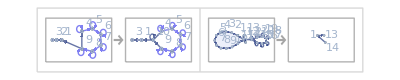

```mathematica
RulePlot[ResourceFunction["WolframModel"][sub1Adsorp],VertexLabels->Automatic]
```

```mathematica
sub1Adsorp[[2]]
```

{{1,2,3,1},{1,4},{5,1},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,6},{12,1}}→{{5,3},{3,4}}

```mathematica
{{1,2,3,1},{3,4},{5,3},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,6},{12,3}}->{{5,2},{2,4}};
```

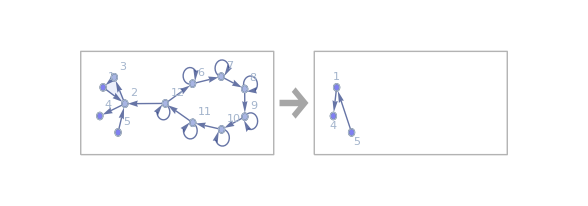

```mathematica
RulePlot[ResourceFunction["WolframModel"][perturb1],VertexLabels->Automatic]
```

Yes, there is unique adsorption. We can use less linking hyperedge stuff as well and get the same result.

```mathematica
numAdsorp = Join[linkingHyperedge,{{1,sizeLinkingHyperedge+1},{sizeLinkingHyperedge+2, 1}}, JoinState[sizeLinkingHyperedge+2, 1, 6]] -> {{sizeLinkingHyperedge +2, sizeLinkingHyperedge}, {sizeLinkingHyperedge, sizeLinkingHyperedge+1}};
```

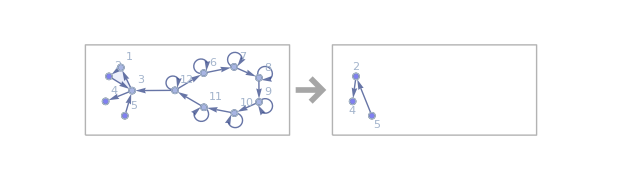

```mathematica
RulePlot[ResourceFunction["WolframModel"][perturb2],VertexLabels->Automatic]
```

this can be incorporated in sub1. there can be a rule for just adsorption,.

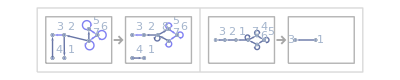

```mathematica
RulePlot[ResourceFunction["WolframModel"][add],VertexLabels->Automatic]
```

```mathematica
ResourceFunction["WolframModelPlot"][JoinState[1, 1,5 ], VertexLabels->Automatic]
```

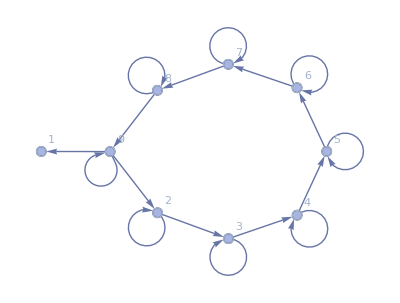

invariant is that the adsorp vertex will always be the maximum vertex of an hyerpgraph before an adbsorping rule is caleld., If we aren’t adsorping, then we can evaluate the function so to speak by outputting the rules and the. Also, another ivnariant is that when we add the new rules, we append without duplicates. It takes the same runtime, and is less tedious to write. So, i the end, I think that’s how normal order evaluation will work.

Hello, how

```mathematica
AppendWithoutDuplicates[list_, element_] := If[MemberQ[list,element], list, Append[list, element]]
```

```mathematica
compileAST[{Bin, "+", 3,4}, False, 0]
```

compileAST[{Bin,+,3,4},False,0]

```mathematica
seeEvol[compileAST[{Bin, "+", 3,4}, False, 0],3]
```

{{2,3},{3,4},{4,1},{6,7},{7,8},{8,9},{9,2},{1,6}}

```mathematica
seeEvol
```

seeEvol

```mathematica
Information[seeEvol]
```

Ok, so we just create another rule called app which will adsorb a number or something. The reason we need this rule is because there’s no way of knowing whether thing to be adsorped is an integer or not. Basically, every argument must have adsorption thing as true. So yeah.

```mathematica
cyclicgraph[n_]:= Join[Table[{i,i+1},{i,0,n-1}],{{n, 0}}]
```

```mathematica
cyclicgraph[n_, start_]:= Join[Table[{i,i+1},{i,start,start+n-1}],{{n+start, start}}]
```

```mathematica
compileAST[x_Integer, adsorpBool_, adsorpVertex_]:= If[adsorpBool, {adsorpVertex-1+cyclicgraph[x, 1],{}}, {cyclicgraph[x,0],{}}]
```

we don’t need to handle x_Symbol because we know it must be in the fun

```mathematica
compileAST[{Bin,"+", x_Integer, y_Integer }, adsorpBool_, adsorpVertex_]:= 
Module[{}, 
If[adsorpBool,
{(adsorpVertex -1)+Join[cyclicgraph[x, 1], {{1, x+2}}, cyclicgraph[y,x+2], JoinState[x+y+2, 1, 2] ],{"addAdsorp", "sub1Adsorp"}}, 
{Join[cyclicgraph[x,1], {{1,x+2}}, cyclicgraph[y, x+2], JoinState[x+y+2, 1, 0]],{"add"}}
 ]
]
```

```mathematica
compileAST[{Bin, "+", x_Integer, y_}, adsorpBool_,  adsorpVertex_]:= 
Module[{yCompile}, 
If[adsorpBool, 
yCompile = compileAST[y, True, sizeLinkingHyperedge + x+6];
(*the adsorp vertex for the next one will become at x+7*)
{(adsorpVertex -1) +Join[Join[cyclicgraph[x,1],JoinState[x+1, 1, 2], {{1, x+7}}, linkingHyperedge+x+6], yCompile[[1]]], DeleteDuplicates[Join[{"addAdsorp", "sub1Adsorp"}, yCompile[[2]]]]},
(*adsorp = False*)
yCompile = compileAST[y, True, sizeLinkingHyperedge + x+4];
{Join[Join[cyclicgraph[x,1],JoinState[x+1, 1, 0], {{1, x+5}}, linkingHyperedge+x+4], yCompile[[1]]], DeleteDuplicates[Join[{"add"}, yCompile[[2]]]]}
]
]
```

```mathematica
compileAST[{Bin, "+", x_, y_Integer}, adsorpBool_, adsorpVertex_]:= compileAST[{Bin, "+", y, x}, adsorpBool, adsorpVertex]
```

```mathematica
compileAST[{Bin,"+", x_, y_ }, adsorpBool_, adsorpVertex_]:= 
Module[{xCompile, yCompile, maxx},
If[adsorpBool,
xCompile = compileAST[x, True,5+sizeLinkingHyperedge];
maxx = Max[xCompile[[1]]];
yCompile = compileAST[y, True, maxx + sizeLinkingHyperedge];{(adsorpVertex -1)+Join[JoinState[1, 1,2],startLink[7, 12],xCompile[[1]], {{1, maxx+1}}, maxx + linkingHyperedge, yCompile[[1]] ],DeleteDuplicates[Join[{"addAdsorp", "sub1Adsorp"}, xCompile[[2]], yCompile[[2]]]]},
xCompile = compileAST[x, True, 3+sizeLinkingHyperedge];
maxx = Max[xCompile[[1]]];
yCompile = compileAST[y, True, maxx + sizeLinkingHyperedge];
{Join[{{3, 3},{3,2},{2,1},{1,3},{2,2},{1,1}, {3,4}}, 3+linkingHyperedge,{{4, maxx + 1}},maxx +linkingHyperedge, xCompile[[1]], yCompile[[1]]], DeleteDuplicates[Join[{"add"}, xCompile[[2]], yCompile[[2]]]]}
 ]
]
```

Let’s see what’s happening

```mathematica
compileAST[{Sub1, x_Integer}, adsorpBool_, adsorpVertex_]:=
If[adsorpBool, {(adsorpVertex-1)+ Join[cyclicgraph[x,1 ], JoinState[x+1, 1, 3]], {"sub1Adsorp"}},
{Join[cyclicgraph[x, 1], JoinState[x+1, 1, 5]],{"sub1"}}
]
```

```mathematica
compileAST[{Sub1, x_}, adsorpBool_, adsorpVertex_]:=
Module[{xCompile},
If[adsorpBool,
(*xCompile = compileAST[x, True,(adsorpVertex-1) + 6+sizeLinkingHyperedge ];*)
xCompile = compileAST[x, True, 6+sizeLinkingHyperedge ];
{(adsorpVertex-1)+Join[JoinState[1,1, 3], startLink[8,sizeLinkingHyperedge],xCompile[[1]] ], DeleteDuplicates[Join[{"sub1Adsorp"}, xCompile[[2]]]]}
,
xCompile = compileAST[x, True, 8+sizeLinkingHyperedge];
{Join[JoinState[0,9, 5 ], 8+linkingHyperedge, xCompile[[1]]], 
DeleteDuplicates[Join[{"sub1"}, xCompile[[1]]]]}
]
]
```

Ok.

```mathematica
compileAST[{IfZero, x_Integer, adsorpBool_, adsorpVertex_}]:=
```

```mathematica
compileAST[IfZero, x_, adsorpBool_, adsorpVertex_]:=
```

How will we do IfZero? well, there should be a rule that allows us to do this. However, the problem was again this thing that we we shouldn’t evaluate the arguments that aren’t used in the function. If I can do that, then I think we can make IfZero. Let’s see whether functions work.

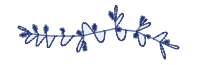
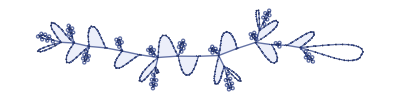
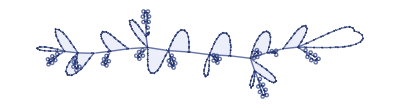
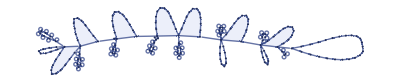
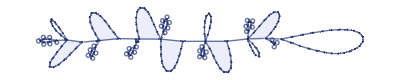
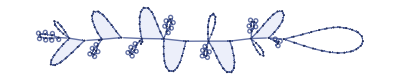
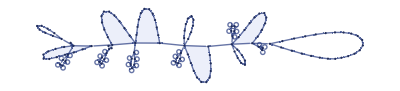
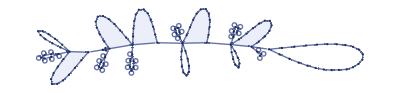

```mathematica
seeEvol[compileAST[{Bin, "+", {Bin, "+", {Bin,"+", 3, 4}, {Bin, "+", {Sub1, 10}, {Sub1, {Bin, "+", {Bin, "+", 2,1}, {Bin,"+", 1, {Sub1, {Sub1, {Sub1, 10}}}}}}}}, {Bin,"+", 12, 10}}, False, 0], 25]
```

```mathematica
(*This will return a list of initial hypergraph and rules. The varsAssocList and varsAdsorptionAssocList will enable us to construct the initial hypergraph.*)
```

If we want to make ifzero without explicitly evaluting teh arguments, then we have to use normal order. How is if zero implemented in ordinary compilers?  Well, yeah, we also evalute the entire thing in the case of if. In ordinary compilers as well. Can we do something in the parser as well? Yeah, it’s not possible. Because usually, we will need to have both things. Note that in orondary compilers, we allocate temporary stack memory at each. Hmmm. Ok, let’s do function application.

Well, there is normal order and applicative order.  IN NORMAL order, we can

```mathematica
compileFunctionHelper[{initialHypergraph_,rules_, varsAdsorptionAssocList_},varsAssocList_ ]:= 10
```

Take care of beta-reduction etc. in parsing. i.e. perform alpha conversions in the parsing step. Here, the var is needed to specify which variable we are talking about. We have to build up the association list.

```mathematica
(*returns a list {initialHypergraph,rules,varsAssocList,varsAdsorptionAssocList} We just want to adsorb stuff pretty quickly and we choose not toe vlaute them separately. we can do ther nomralmthing however that will be very slow. Basically, the thing we have to do will depedn on the varsAdsorptionAssoclist. So there must be a separate case for when the association list Empty*)
```

varsAssocList, varsAdsorptionAssociList

The var tells us which variable is being talked about. This is because we can only apply a function to something.  compileASTHelper[(App (Fun x x+5) (+ 10 12), x)]. We get that compileASTHelper[5+x, x -> (+ 10 12) ]. Then, what? Then we would have an adsorption. This is precisely normal order. This is because if I have (λx. 5)(expression). This does not evaluate the expression... this makes the leftmost outermost Redex. This means that Y-combinator should work like magic! And it would be cool to visualise it. Let’s prove it using structural induction:

(λx. x)[ARG] -> ARG.

Yes, this makes sense....or does it.

Invariant: compileASTHelper returns {initialHypergraph,rules, varsAdsorptionAssocList}.

data Ast  = 	   num
          |     var
		 	 	|	 	(Bin “+“ Ast Ast)
		 	 	|    (Sub1 Ast)
		 	 	|	 	(Fun (var) expr)
		 	 	|	 	(App Ast Ast var)
		 	 	|	 	(IfZero Ast Ast Ast)
		 	 	|	 	(Rec ((var Ast)) Ast) (maybe, maybe not).

Assumption that there are no free variables in every expression. So we can compile combinators. Ok, let;s do that. var must occur in a fun. fun cannot occur by itself. Make currying in the parser

```mathematica
compileAST[{App, {Fun, var_, AST_},ARG_}, adsorpBool_, adsorpVertex_]:= compileFunctionHelper[compileASTHelper[AST, adsorpBool, adsorpVertex], {var -> AST}]
```

```mathematica
If["string"=="String",4,5]
```

5

```mathematica
AppASTtoAexp[AST_, acc_]:= 
If[ToString[AST[[1]]] == "Fun", If[Length[acc] == 1, {AST[[3]], {AST[[2]] -> acc[[1]]} },{#[[1]], Join[{AST[[2]]->acc[[1]]}, #[[2]]]}&[AppASTtoAexp[AST[[3]], Drop[acc, 1]]]],
AppASTtoAexp[AST[[2]], Prepend[acc, AST[[3]]]]
]
```

I don’t think Ifzero can be implemented...Then how will we parse ifzero? Maybe we don’t need to parse it. Maube the rest is a turing complete language? (then we should be able to parse it).

```mathematica
compileAST[{App, {Fun, var_, AST_},ARG_}, adsorpBool_, adsorpVertex_]:= compileFunctionHelper[compileASTHelper[AST, adsorpBool, adsorpVertex], {var -> AST}]
```

```mathematica
compileAST[{App, {Fun, x, {Bin, "+", x,5}}, 9}, False]
```

compileAST[{App,{Fun,x,{Bin,+,x,5}},9}]

```mathematica
compileASTHelper[{Bin, "+", {Bin, "+" ,{Sub1, x},u},{Bin, "+", {Sub1, x}, {Sub1, y}}}, False, 0]
```

{{{1,1},{2,2},{3,3},{1,2},{2,3},{3,1},{3,0},{0,4,5,6,7,8,9,10,11,12,13,14,0},{0,60},{60,61,62,63,64,65,66,67,68,69,70,71,60},{15,15},{16,16},{17,17},{18,18},{19,19},{15,16},{16,17},{17,18},{18,19},{19,15},{19,14},{14,20,21,22,23,24,25,26,27,28,29,30,14},{14,31},{31,32,33,34,35,36,37,38,39,40,41,42,31},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{43,44},{44,45},{45,46},{46,47},{47,48},{48,43},{48,42},{42,49,50,51,52,53,54,55,56,57,58,59,42},{72,72},{73,73},{74,74},{75,75},{76,76},{72,73},{73,74},{74,75},{75,76},{76,72},{76,71},{71,77,78,79,80,81,82,83,84,85,86,87,71},{71,105},{105,106,107,108,109,110,111,112,113,114,115,116,105},{88,88},{89,89},{90,90},{91,91},{92,92},{93,93},{88,89},{89,90},{90,91},{91,92},{92,93},{93,88},{93,87},{87,94,95,96,97,98,99,100,101,102,103,104,87},{117,117},{118,118},{119,119},{120,120},{121,121},{122,122},{117,118},{118,119},{119,120},{120,121},{121,122},{122,117},{122,116},{116,123,124,125,126,127,128,129,130,131,132,133,116}},{addAdsorp,sub1Adsorp},{u→31,x→46,x→34,y→63}}

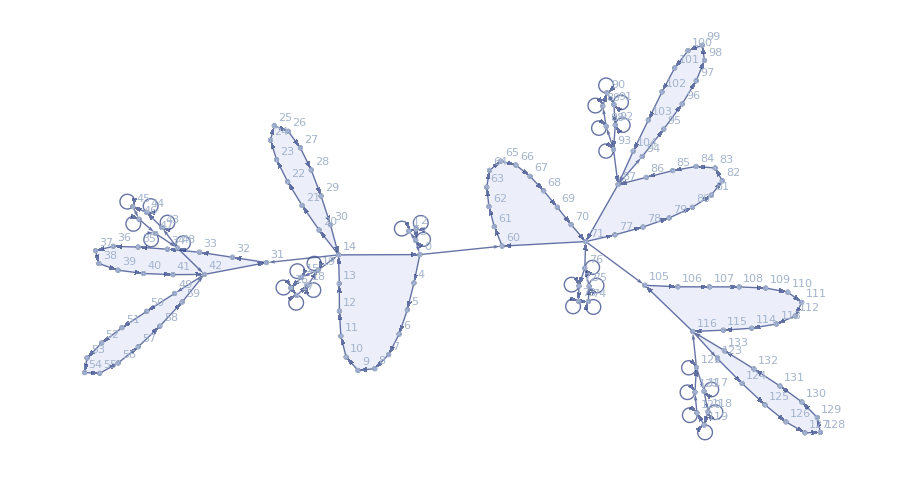

```mathematica
ResourceFunction["WolframModelPlot"][%402[[1]],VertexLabels-> Automatic]
```

this is wrong.=

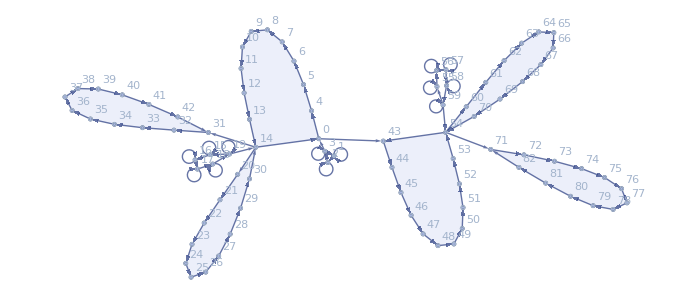

```mathematica
ResourceFunction["WolframModelPlot"][%398[[1]],VertexLabels-> Automatic]
```

there’s an erorr in the aboe.

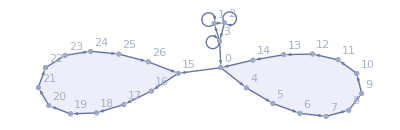

```mathematica
ResourceFunction["WolframModelPlot"][%372[[1]],VertexLabels-> Automatic]
```

```mathematica
compileASTHelper[{Bin, "+", 9,5}, False, 0]
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1},{1,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,11},{17,17},{18,18},{19,19},{17,18},{18,19},{19,17},{19,1}},{add},{}}

```mathematica
compileAST[{App, AST_, ARG_}, adsorpBool_, adsorpVertex_]:= compileFunctionHelper[compileASTHelper[#[[1]], adsorpBool, adsorpVertex],#[[2]]]&[AppASTtoAexp[AST]]
```

```mathematica
compileASTHelper[x_Integer, adsorpBool_, adsorpVertex_]:=If[adsorpBool, {adsorpVertex-1 +cyclicgraph[x,1], {}, {}},{cyclicgraph[x,0],{},{}}]
```

```mathematica
compileASTHelper[x_Symbol,adsorpBool_, adsorpVertex_]:=
If[adsorpBool, {{}, {}, {x -> adsorpVertex}}]
```

Compile ASTHelper returns {intial hypergraph, rules, varsAdsorption AssocList}. In the above, the initial hypergraph is empty because the we are ust adsorping the symbol only.

```mathematica
compileASTHelper[{Bin, "+", x_Integer, y_Integer}, adsorpBool_, adsorpVertex_]:=
Module[{}, 
If[adsorpBool, 
{(adsorpVertex -1)+Join[cyclicgraph[x, 1], {{1, x+2}}, cyclicgraph[y,x+2], JoinState[x+y+2, 1, 2] ],{"addAdsorp", "sub1Adsorp"}, {}}, 
{Join[cyclicgraph[x,1], {{1,x+2}}, cyclicgraph[y, x+2], JoinState[x+y+2, 1, 0]],{"add"}, {}}
 ]]
```

```mathematica
compileASTHelper[{Bin, "+", x_Integer, y_}, adsorpBool_, adsorpVertex_]:=
Module[{yCompile}, 
If[adsorpBool,
If[Not[ListQ[y]], 
{adsorpVertex -1+Join[cyclicgraph[x,1],JoinState[x+1, 1, 2], {{1, x+7}}, linkingHyperedge+x+6],{"addAdsorp", "sub1Adsorp"}, {y -> adsorpVertex -1 + sizeLinkingHyperedge + x+6}}, 
(*yCompile = compileAST[y, True,adsorpVertex -1 + sizeLinkingHyperedge + x+6, varsAssocList];*)
yCompile = compileASTHelper[y, True,sizeLinkingHyperedge + x+6];
{adsorpVertex -1 +Join[Join[cyclicgraph[x,1],JoinState[x+1, 1, 2], {{1, x+7}}, linkingHyperedge+x+6], yCompile[[1]]], DeleteDuplicates[Join[{"addAdsorp", "sub1Adsorp"}, yCompile[[2]]]],yCompile[[3]]}
  ],
If[Not[ListQ[y]], 
{Join[cyclicgraph[x,1],JoinState[x+1, 1, 0], {{1, x+5}}, linkingHyperedge+x+4],{"add"}, {y -> sizeLinkingHyperedge + x+4}},
yCompile = compileASTHelper[y, True,sizeLinkingHyperedge + x+4];
{Join[Join[cyclicgraph[x,1],JoinState[x+1, 1, 0], {{1, x+5}}, linkingHyperedge+x+4], yCompile[[1]]], DeleteDuplicates[Join[{"add"}, yCompile[[2]]]],yCompile[[3]]}
]
  ]
]
```

```mathematica
compileASTHelper[{Bin, "+", x_, y_Integer}, adsorpBool_, adsorpVertex_]:= compileASTHelper[{Bin, "+", y, x}, adsorpBool,adsorpVertex]
```

```mathematica
Head[x] == Symbol
```

True

```mathematica
ListQ[x]
```

False

```mathematica
SymbolQ
```

```mathematica
List != Symbol
```

List≠Symbol

```mathematica
Not[True]
```

False

Here x is either a symbol or a list. So yeah. we have already checked whether we have integers or not.

```mathematica
compileASTHelper[{Bin,"+", x_, y_ }, adsorpBool_, adsorpVertex_]:= 
Module[{xCompile, yCompile, maxx},
If[adsorpBool,
If[Not[ListQ[x]], If[Not[ListQ[y]],{adsorpVertex-1 +Join[JoinState[1, 1, 2], startLink[7,12], {{1,6+sizeLinkingHyperedge}},5+sizeLinkingHyperedge+linkingHyperedge], {"addAdsorp", "sub1Adsorp"},{{x -> (adsorpVertex -1) +5 + sizeLinkingHyperedge, y -> (adsorpVertex-1) +5 + (2*sizeLinkingHyperedge)}} } ,
yCompile = compileASTHelper[y, True,  5 + (2*sizeLinkingHyperedge)];
{adsorpVertex-1 +Join[JoinState[1, 1, 2], startLink[7,12], {{1,6+sizeLinkingHyperedge}},5+sizeLinkingHyperedge+linkingHyperedge, yCompile[[1]]],DeleteDuplicates[Join[{"addAdsorp","sub1Adsorp"}, yCompile[[2]]]], Join[{x-> (adsorpVertex -1) +5 + sizeLinkingHyperedge}, yCompile[[3]]] }], If[Not[ListQ[y]], 
compileASTHelper[{Bin, "+", y, x},adsorpBool, adsorpVertex], 
(*both not symbols. So *)
xCompile = compileASTHelper[x, True,5 + sizeLinkingHyperedge];
maxx = Max[xCompile[[1]]];
yCompile = compileASTHelper[y, True, maxx + sizeLinkingHyperedge];
{(adsorpVertex-1)+ Join[JoinState[1, 1, 2], startLink[7,12], {{1, maxx + 1}},maxx + linkingHyperedge, xCompile[[1]], yCompile[[1]]], DeleteDuplicates[Join[{"addAdsorp", "sub1Adsorp"}, xCompile[[2]], yCompile[[2]]]], Join[xCompile[[3]], yCompile[[3]]]}]],
If[Not[ListQ[x]], If[Not[ListQ[y]],{adsorpVertex-1 +Join[JoinState[1, 1, 0], startLink[5,12],{{1,4+sizeLinkingHyperedge}},3+sizeLinkingHyperedge+linkingHyperedge], {"addAdsorp", "sub1Adsorp"}, {{x -> (adsorpVertex -1) +3 + sizeLinkingHyperedge, y -> (adsorpVertex-1) +3+ (2*sizeLinkingHyperedge)}} } ,
(*x symbol, y not symbol -- but y mayb contain symbols*)
yCompile = compileASTHelper[y, True,  3 + (2*sizeLinkingHyperedge)];
{adsorpVertex-1 +Join[JoinState[1, 1, 0], startLink[5,12],{{1,4+sizeLinkingHyperedge}},3+sizeLinkingHyperedge+linkingHyperedge, yCompile[[1]]],DeleteDuplicates[Join[{"addAdsorp","sub1Adsorp"}, yCompile[[2]]]], Join[{x-> (adsorpVertex -1) +3 + sizeLinkingHyperedge}, yCompile[[3]]] }], If[Not[ListQ[y]], 
compileASTHelper[{Bin, "+", y, x},adsorpBool, adsorpVertex], 
(*both not symbols*)
xCompile = compileASTHelper[x, True, 3 + sizeLinkingHyperedge];
maxx = Max[xCompile[[1]]];
yCompile = compileASTHelper[y, True, maxx + sizeLinkingHyperedge];
{(adsorpVertex-1)+ Join[JoinState[1, 1, 0], startLink[5,12], {{1, maxx + 1}},maxx + linkingHyperedge, xCompile[[1]], yCompile[[1]]], DeleteDuplicates[Join[{"addAdsorp", "sub1Adsorp"}, xCompile[[2]], yCompile[[2]]]], Join[xCompile[[3]], yCompile[[3]]] }
(*both not symbols*)]]
 ]
]
```

Have I done the the non-adsorption case? Gosh.

I think this is correct.

```mathematica
compileASTHelper[{Sub1, x_Integer}, adsorpBool_, adsorpVertex_]:=If[adsorpBool, {adsorpVertex-1+ Join[cyclicgraph[x,1 ], JoinState[x+1, 1, 3]], {"sub1Adsorp"},  {}},
{Join[cyclicgraph[x, 1], JoinState[x+1, 1, 5]],{"sub1"}, {}}
]
```

```mathematica
compileASTHelper[{Sub1, x_}, adsorpBool_, adsorpVertex_]:=
Module[{xCompile},
If[adsorpBool,
If[Head[x] == Symbol,  
{(adsorpVertex - 1) +Join[JoinState[1,1,3],startLink[8,12]], {"sub1Adsorp"},{x -> (adsorpVertex - 1)+6+sizeLinkingHyperedge}},
xCompile = compileASTHelper[x, True, 6+sizeLinkingHyperedge ];
{(adsorpVertex - 1) +Join[JoinState[1,1,3],startLink[8,12], xCompile[[1]]],DeleteDuplicates[Join[{"sub1Adsorp"}, xCompile[[2]]]], xCompile[[3]]}
],
If[Head[x] == Symbol, 
{Join[JoinState[1,1,5],startLink[10,12]], {"sub1"}, {x -> 8+sizeLinkingHyperedge}},
xCompile = compileASTHelper[x, True, 8 + sizeLinkingHyperedge];
{Join[JoinState[1, 1, 5], startLink[10,12], xCompile[[1]]], DeleteDuplicates[Join[{"sub1"}, xCompile[[2]]]], xCompile[[3]]}
]
]
]
```

Ok, now

Compile function helper.

This will be done imperatively.

I can create a do loop. The hypergraph must not be recreated.

I will  have {initialHypergraph_,rules_, varsAdsorptionAssocList_},varsAssocList_. This wil re3utn the initial hypergraph and rules. So the rules will be thos eexisting plius the ones usined to the computer the variables. Lol. this is easy.

Wait, this can be tail recursively on the varsAdsoprionlist. Well, it is impossilbe to get repeats. Let’s test.

then, do recursion using Y combinator

test stuff

done!]

### botes

essentially, parsing might be buiklding an entier normal order evaluator.

One option is to just do the evaluation on those adsorption towers separately. ThI think that is the only option, because they is no other way of doing that. It’s going to be very hard otherwise. Actually, that’s the better way as it will involve less computation and that can actually be done.

So, consider functions being completely implemented. Applications of functions are also easy!

But it is worth trying to see whether my Y-combinator will work or not. Because normal order evaluation should make things work. Note that I can “cheat” on the compiler by parsing into normal order, which is technically not cheating. I wonder what formal definitions could you make on cheating on a compiler.

Assume that I am successful in doing recursion using the Y-combinator. Then what would I need to use? Well, in normal order, I will just substitute things in parsing. That would be equivalently computationally expensive in hypergraph rewriting  because in applicative order, I am doing the computation of the argument on each adsorption tower.

So let’s see whether recursion will actualyl work. In normal order, I would not have functions as ASTS. Just bins, sub1, nums, and ifzero. That’ll be pretty cool